## Import

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
pathSRC="../src/";
Get[pathSRC<>"basic.m"];
Get[pathSRC<>"dftb.m"];
Get[pathSRC<>"negf.m"];
Get[pathSRC<>"xyz.m"];

Get["../skf/auorg.E.m"];
Get["../skf/auorg.V.mx"];
Get["../skf/auorg.S.mx"];
```

## Ham gen

```mathematica
moleName="mcpp_jt.centered";
{atoms,types,bonds}=ImportXYZ[moleName<>".xyz"];
natom=Length[atoms]
```

136

```mathematica
h=DFTBSolver2[atoms,types];
s=DFTBSolver2[atoms,types,"S"];
```

## MOL

```mathematica
atomsM=atoms⟦35;;102⟧;
typesM=types⟦35;;102⟧;
hM=DFTBSolver2[atomsM,typesM];
sM=DFTBSolver2[atomsM,typesM,"S"];
{eval,evec}=MyEigensystem[{hM,sM}];
{EHOMO,ELUMO,EF,EGap,NHOMO}=GetHOLU[eval,evec,atomsM,typesM]
EF
```

{-4.82859,-4.73366,-4.78112,0.0949291,107}

-4.78112

## Import Surface

```mathematica
ΣL=<<"surface/SigmaL-S1-48.m";
ΣR=<<"surface/SigmaR-S1-48.m";
```

```mathematica
norb=Length[h]
```

822

```mathematica
ΣL=-0.1I DiagSparseMatrix[Range[1,25*9],norb];
ΣR=-0.1I DiagSparseMatrix[norb+1-Range[1,25*9],norb];
```

```mathematica
Total[ΣR,2]
```

-225 ⅈ

## Transport

```mathematica
{emin,emax,estep}={EF-2,EF+2,0.02};
et=Table[
{ϵ-EF,NEGFSystemWBΣS[ϵ,h,s,ΣL,ΣR]⟦1⟧},
{ϵ,emin,emax,estep}
]
```

{{-2.,0.160099},{-1.98,0.0293015},{-1.96,0.0717528},{-1.94,0.111872},{-1.92,0.453101},{-1.9,0.420259},{-1.88,0.395684},{-1.86,0.18625},{-1.84,0.942105},{-1.82,0.786195},{-1.8,1.05796},{-1.78,0.447501},{-1.76,0.276153},{-1.74,0.464747},{-1.72,0.836441},{-1.7,0.275947},{-1.68,0.148487},{-1.66,0.725406},{-1.64,0.924917},{-1.62,0.685959},{-1.6,0.522864},{-1.58,0.300174},{-1.56,0.284413},{-1.54,0.980144},{-1.52,0.850001},{-1.5,0.602415},{-1.48,0.423543},{-1.46,0.291147},{-1.44,0.939182},{-1.42,0.267526},{-1.4,0.635344},{-1.38,0.75617},{-1.36,0.767076},{-1.34,0.702111},{-1.32,0.433174},{-1.3,0.450212},{-1.28,0.534773},{-1.26,0.68644},{-1.24,0.667373},{-1.22,0.966423},{-1.2,0.324615},{-1.18,0.828016},{-1.16,0.472428},{-1.14,0.859521},{-1.12,0.338642},{-1.1,0.286041},{-1.08,0.213377},{-1.06,0.270052},{-1.04,0.427417},{-1.02,0.316063},{-1.,0.0777945},{-0.98,0.210626},{-0.96,0.305834},{-0.94,0.0380222},{-0.92,0.0125431},{-0.9,0.0609301},{-0.88,0.0310847},{-0.86,0.00667072},{-0.84,0.00321048},{-0.82,0.00130636},{-0.8,0.000509403},{-0.78,0.000552291},{-0.76,0.000482088},{-0.74,0.000416428},{-0.72,0.00206082},{-0.7,0.00204239},{-0.68,0.0018964},{-0.66,0.00211336},{-0.64,0.00266615},{-0.62,0.00302386},{-0.6,0.00379485},{-0.58,0.00257982},{-0.56,0.00116701},{-0.54,0.000867677},{-0.52,0.00175661},{-0.5,0.00512399},{-0.48,0.00263192},{-0.46,0.00205435},{-0.44,0.00188816},{-0.42,0.00189722},{-0.4,0.00203978},{-0.38,0.00233955},{-0.36,0.00288125},{-0.34,0.00386329},{-0.32,0.005838},{-0.3,0.0131145},{-0.28,0.0573762},{-0.26,0.0325637},{-0.24,0.0328162},{-0.22,0.0312207},{-0.2,0.0268498},{-0.18,0.0229401},{-0.16,0.0209587},{-0.14,0.0211456},{-0.12,0.0238829},{-0.1,0.0303268},{-0.08,0.0433483},{-0.06,0.067698},{-0.04,0.0564821},{-0.02,0.0279409},{0.,0.016813},{0.02,0.0109883},{0.04,0.00745134},{0.06,0.00517488},{0.08,0.00366442},{0.1,0.00264632},{0.12,0.00195239},{0.14,0.00147373},{0.16,0.00113899},{0.18,0.000901467},{0.2,0.000730582},{0.22,0.000606218},{0.24,0.000515037},{0.26,0.000448148},{0.28,0.000399627},{0.3,0.000365606},{0.32,0.000343739},{0.34,0.000332938},{0.36,0.000333366},{0.38,0.000346734},{0.4,0.000377097},{0.42,0.000432579},{0.44,0.00052883},{0.46,0.000694447},{0.48,0.000968514},{0.5,0.00132663},{0.52,0.00149739},{0.54,0.00130451},{0.56,0.00106522},{0.58,0.000989439},{0.6,0.001166},{0.62,0.00182622},{0.64,0.00252941},{0.66,0.0018955},{0.68,0.00157755},{0.7,0.00177028},{0.72,0.00248265},{0.74,0.0041003},{0.76,0.00720706},{0.78,0.00967319},{0.8,0.00724405},{0.82,0.00412031},{0.84,0.00238487},{0.86,0.00154334},{0.88,0.00113261},{0.9,0.000911571},{0.92,0.000781129},{0.94,0.000709377},{0.96,0.000693002},{0.98,0.000731458},{1.,0.000780642},{1.02,0.000819219},{1.04,0.000914309},{1.06,0.00112452},{1.08,0.00145454},{1.1,0.00176701},{1.12,0.00192888},{1.14,0.00205496},{1.16,0.00230092},{1.18,0.00276076},{1.2,0.00352427},{1.22,0.00470697},{1.24,0.00642005},{1.26,0.0086352},{1.28,0.0109375},{1.3,0.0125182},{1.32,0.0128707},{1.34,0.0123903},{1.36,0.0119651},{1.38,0.0121784},{1.4,0.0130924},{1.42,0.0147868},{1.44,0.0183723},{1.46,0.0278127},{1.48,0.0546887},{1.5,0.130829},{1.52,0.124416},{1.54,0.0670017},{1.56,0.0802441},{1.58,0.194848},{1.6,0.730001},{1.62,0.198194},{1.64,0.0636026},{1.66,0.0369053},{1.68,0.0321711},{1.7,0.0382799},{1.72,0.058659},{1.74,0.101755},{1.76,0.171045},{1.78,0.813453},{1.8,0.161279},{1.82,0.0940964},{1.84,0.0810788},{1.86,0.0817957},{1.88,0.0876955},{1.9,0.0963754},{1.92,0.108489},{1.94,0.123495},{1.96,0.124036},{1.98,0.0859293},{2.,0.0469168}}

## Plot

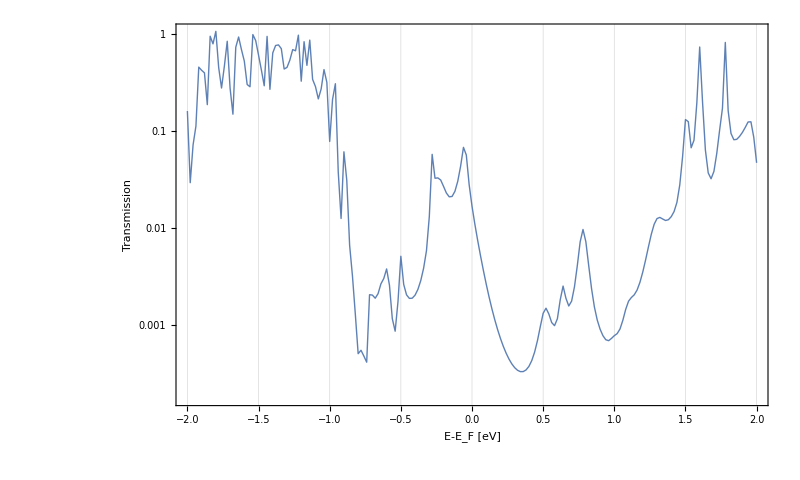

```mathematica
ListLogPlot[{et},GridLines->{eval-EF,None},
FrameLabel->{"E-E_F [eV]"," Transmission "},
Frame->True,
AspectRatio->0.6,
(*PlotLegends->Placed[{"BZ","CJ"},{0.55,0.8}],*)
Joined->True,
PlotStyle->Thick,
ImageSize->{800,500},
Axes->False,
styles]
```